## Useful functions

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,Magnification->1.6};
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/31_resonances/code

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=(-1.)^l z SphericalBesselY[l,z];
```

```mathematica
FunctionExpand[RiccatiBesselJ[z,0]]
FunctionExpand[RiccatiBesselN[z,0]]
FunctionExpand[RiccatiBesselJ[z,1]]
FunctionExpand[RiccatiBesselN[z,1]]
```

Sin[z]

-1. Cos[z]

z (-Cos[z]/z+Sin[z]/z^2)

-1. z (-Cos[z]/z^2-Sin[z]/z)

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

LEC=(Λ,a_(3-1)^(S-wave) [fm],C_(2-body) [MeV],C_(3-body) [MeV])
the triton-proton S-wave scattering length is used to calibrate the core parameter and
was obtained by R. Lazauskas.

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import[NotebookDirectory[]<>"../data/a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];
LECsUNITmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_univ_Rimas-Martin.dat","Table"][[2;;]];

activeLEC=LECsUNITmartinrimas(*LECsNUCLmartinrimas[[All,{1,2,3}]]*);
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for TRIMER-FERMION (ABC-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
Integrate[Subscript[c, 1] Subscript[c, 2] Exp[-(Subscript[α, 1]+Subscript[α, 2]) r^2],{r,-Infinity,Infinity},Assumptions->{Subscript[α, 1]∈Reals,Subscript[α, 1]>0,Subscript[α, 2]∈Reals,Subscript[α, 2]>0}]
```

(√π c_1 c_2)/(√(α_1+α_2))

```mathematica
NormTF[core_?ArrayQ]:=1./Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Pi/(core[[i]][[2]]+core[[j]][[2]]))^1.5,{i,Length[core]},{j,Length[core]}]]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_]:=Block[{eta2,eta3,w2,w3},
eta2=2. Cc/(2. (Aa+Bb)(3. Aa+3. Bb+2. lam))^(3./2.);
w2=3. (Aa+Bb) lam/(3. (Aa+Bb)+2. lam);
eta3=Dd/(6. (Aa+Bb)^2+16. (Aa+Bb) lam+2. lam^2)^(3./2.);
w3=(3. (Aa+Bb) lam ((Aa+Bb)+2. lam)/(3. (Aa+Bb)^2+8. (Aa+Bb) lam+lam^2));
eta2 Exp[-w2 r^2]+eta3  Exp[-w3 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(27./64.)(2 (Aa+Bb))^(-3./2.) (1./TwoMyOverHBsq);
a1=(Aa+9. Bb) 3./32.;
b1=(Aa+Bb) 9./16.;
c1=(9. Aa+Bb) 3./32.;

zeta2=-27./32. Cc/(2. (Aa+Bb)+lam)^(3./2.);
zeta3=-27./64. Dd/(2  (Aa+Bb)+5 lam)^(3./2.);

a2=3. (Aa^2+9. Bb^2+10. Aa Bb+(14. Aa+18. Bb) lam)/(16. (2. (Aa+Bb)+lam));
b2=18. (Aa+Bb) ((Aa+Bb)+2. lam)/(16. (2. (Aa+Bb)+lam));
c2=3. (9. Aa^2+Bb^2+10. Aa Bb+(6. Aa+2. Bb) lam)/(16. (2. (Aa+Bb)+lam));

a3=3. (Aa^2+9. Bb^2+10. Aa Bb+(16. Aa+36. Bb) lam+27. lam^2)/(16. (2. (Aa+Bb)+5. lam));
b3=18. ((Aa+Bb)^2+4. (Aa+Bb) lam+3. lam^2)/(16. (2. (Aa+Bb)+5. lam));
c3=3. (9. Aa^2+Bb^2+10. Aa Bb+(24. Aa+4. Bb) lam+3. lam^2)/(16. (2 (Aa+Bb)+5. lam));

-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV];
The core wave function is parametrized via the "a0={{c_1,α_1},{c_2,α_2},...,{c_N,α_N}}" array:
ϕ_core=(∑^N)_(i=1)c_i·e_^(-α_i/2∏_j (r^-)_j^2)

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=NormTF[a00]^2;

Wmat=ConstantArray[0,{Npoints,Npoints}];

prefac=(*(4 π)^1.5*)1.;
Do[
(*If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,*)

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];

wmat=Table[-prefac hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 
(*Print[(Chop[cij (wmat)])[[1;;4,1;;4]]//MatrixForm];*)
Wmat=Wmat+cij (amat+wmat);

(*]*)
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];
Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

numerical and physical parameters

```mathematica
nf={6,4}; (* number form for printing, only *)
k0FM=0.01;  (*initial momentum*)

hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
sy={"nuclear","unitary"}[[2]];
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV     ℏ^2/(2 SubscriptBox[μ, A = 4]) = ",hbar^2/(2 (Mm^2/(2 Mm)))," MeV·fm^2     ℏ^2/(2 SubscriptBox[μ, A = 2]) = ",1/mh2]
λRange=Range[1,Length[activeLEC]];
```

E_0 = 0.00276473 MeV     ℏ^2/(2 SubscriptBox[μ, A = 4]) = 41.471 MeV·fm^2     ℏ^2/(2 SubscriptBox[μ, A = 2]) = 27.6473

```mathematica
findLogDivisions[{xmin_,xmax_},n_Integer]:=10^FindDivisions[Log10@{xmin,xmax},n]

GetERE[x_,l_]:=Module[{localcore=x,locall=l},

core=localcore;

dataS={};dataP={};
tanDsL={};tanDpL={};
tanDs={};tanDp={};

SetSharedVariable[tanDs,tanDp];

ParallelDo[
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecular[rr,nGrid,momFM,0,locall,C0,D0,core,mh2];
TanDelPwave=SolveSecular[rr,nGrid,momFM,1,locall,C0,D0,core,mh2];
AppendTo[tanDs,{energ,TanDelSwave}];
AppendTo[tanDp,{energ,TanDelPwave}];
,{energ,ErangeMeV}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
tanDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
(*AppendTo[tanDsL,tnDs];
AppendTo[tanDpL,tnDp];*)
(*Extract the ERE Parameters*)
Lrel = 0;
dataS=Transpose[{Sqrt[mh2 ErangeMeV],Sqrt[mh2 ErangeMeV]/Re[tanDs⟦All,2⟧]}];
EreS=Fit[dataS⟦f1;;f2⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
Lrel = 1;
dataP=Transpose[{Sqrt[mh2 ErangeMeV],Sqrt[mh2 ErangeMeV]^3/Re[tanDp⟦All,2⟧]}];
EreP=Fit[dataP⟦f1;;f2⟧,{1,p^2},p];
a1tf=-Coefficient[EreP,p,0]^-1;
r1tf= Coefficient[EreP,p,2]*2.;
(*Print["dataS = ", dataS];*)
{a0tf,r0tf,a1tf,r1tf,dataS,dataP}
]
```

```mathematica
PlotERE:=Module[{},(*Plot the Phaseshifts for each α and C that I used*)
phaseS=Transpose[{tanDs⟦All,1⟧, ArcTan[tanDs⟦All,2⟧]}];
phaseP=Transpose[{tanDp⟦All,1⟧, ArcTan[tanDp⟦All,2⟧]}];
(*---------*)
Tfits=(Fit[dataS⟦1;;Min[10,Length[dataS]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTS=dataS;dataTS⟦All,2⟧=dataTS⟦All,2⟧^-1 ;
Polesp=(p/.NSolve[Tfits-ⅈ p==0,{p}]) ; (*find pole positions*) PolesE=hbar^2 Polesp^2 / (2 μ);
Print["S Pole Poitions in momentum: ", Polesp];
Print["S Pole Poitions in energy:   ", PolesE];
(*---------*)
Tfitp=(Fit[dataP⟦1;;Min[10,Length[dataP]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTP=dataP;dataTP⟦All,2⟧=dataTP⟦All,2⟧^-1 ;
Polepp=(p/.NSolve[Tfitp-ⅈ p^3==0,{p}]) ; (*find pole positions*) PolepE=hbar^2 Polepp^2 / (2 μ);
Print["P Pole Poitions in momentum: ", Polepp];
Print["P Pole Poitions in energy:   ", PolepE];
Print[Tfits];
Print[Tfitp];
GraphicsGrid[{{
Show[{ Plot[-(1/a0tf)+(1/2)r0tf k^2,{k,0,dataS⟦-1,1⟧}],ListPlot[dataS,PlotRange->{{dataS⟦1,1⟧,dataS⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K CotTan[δ_(S - wave)] [fm^-1]"},PlotStyle->"Red", PlotLabel->" S-wave KCotδ compared with -1/a0+1/2r0 k^2"]
,
Show[{ Plot[-(1/a1tf)+(1/2)r1tf k^2,{k,0,dataP⟦-1,1⟧}],ListPlot[dataP,PlotRange->{{dataP⟦1,1⟧,dataP⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K^3 CotTan[δ_(S - wave)] [fm^-3]"},PlotStyle->"Red",PlotLabel->" P-wave K^3Cotδ compared with -1/a0+1/2r0 k^2"]

},
{
Show[ListPlot[dataTS],Plot[Tfits^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"],
Show[ListPlot[dataTP],Plot[Tfitp^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"]

}
},ImageSize->1000]//Print
]
```

## Import density and fit wavefunctions

```mathematica
tailweight=0;
wflambdasN={1.0,2.0,3.0,4.0,6.0,8.0,10.0};
Martinϕnucl=Cases[Import["../data/abc_u_"<>ToString[NumberForm[#,{12,1}]]<>"_binf_r1b.dnst","Table"],{_?NumberQ,___}]&/@wflambdasN;
MϕN=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧]}]&/@Martinϕnucl;
wflambdasU={1.5,2.0,3.0,4.0,6.0,8.0,10.0};
Martinϕunit=Cases[Import["../data/abc_univ_"<>ToString[NumberForm[#,{12,1}]]<>"_binf_r1b.dnst","Table"],{_?NumberQ,___}]&/@wflambdasU;
MϕU=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧]}]&/@Martinϕunit;
If[sy=="unitary",
Mϕ=MϕU;
wflambdas=wflambdasU;
,
Mϕ=MϕN;
wflambdas=wflambdasN;]
```

λ=1.5  , core={{0.0518707,0.230424},{0.00667568,0.076468},{0.10683,1.81624},{0.141054,0.671358}}

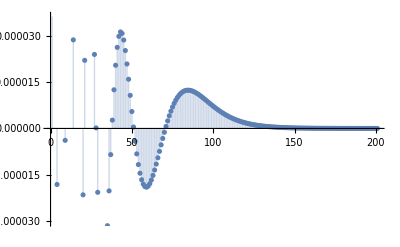

λ=2.  , core={{0.0454719,0.223235},{0.144003,0.681275},{0.167614,2.09822},{0.00559148,0.0743594}}

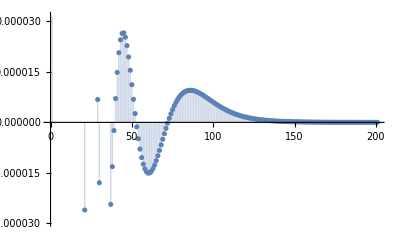

λ=3.  , core={{0.296311,2.09955},{0.0174684,0.114449},{0.0621954,0.463435},{0.0601019,0.464489}}

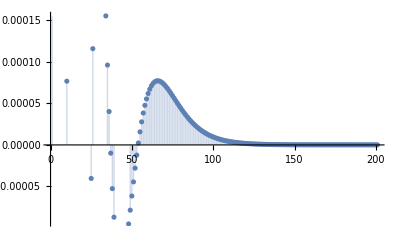

λ=4.  , core={{0.0931665,0.275992},{0.0345229,1.68181},{0.0252575,1.70581},{0.3285,2.09533}}

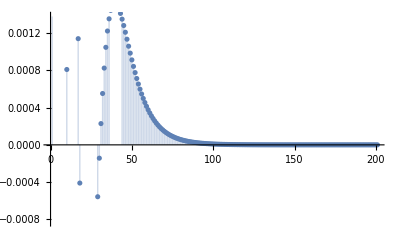

λ=6.  , core={{0.435559,2.1},{0.0424987,0.320602},{0.0424987,0.320602},{0.00605621,0.0769025}}

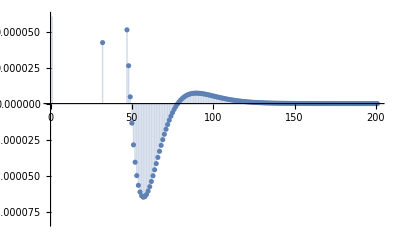

λ=8.  , core={{0.0380442,0.288375},{0.0380442,0.288375},{0.00397222,0.0659831},{0.473733,2.1}}

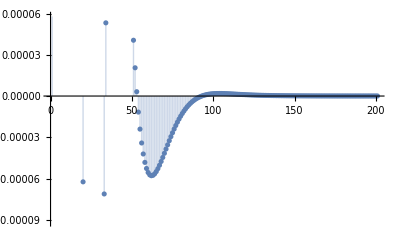

λ=10.  , core={{0.0351526,0.269246},{0.0028255,0.058772},{0.0351526,0.269246},{0.500476,2.1}}

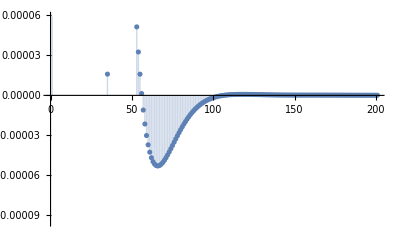

```mathematica
nk=4;

rmip=0.0;
rmap=21;

wfCores={};
wfs={};
w1=1;
amax=10^1;amin=0;
bmin=0.0;bmax=2.1;
w2=Min[Length[#]&/@Mϕ];
Do[
data=Mϕ[[ll]][[w1;;w2]];

modelGauss={Sum[aLn@i Exp[-bLn@i rrel^2],{i,nk}],Table[{amin<aLn@i <amax,bmin<bLn@i <bmax},{i,nk}]};
nlmLABC=NonlinearModelFit[data,modelGauss,Flatten[Table[{{aLn@i,RandomReal[{-0.1,0.1}]},{bLn@i,RandomReal[{0.0001,0.25}]}},{i,nk}],1],rrel,Weights->((#+1)^3&/@data[[All,1]])];
nlresi=nlmLABC["FitResiduals"];
(*modelGauss=Sum[aLn@i Exp[-bLn@i rrel^2],{i,nk}];
nlmLABC=NonlinearModelFit[data,modelGauss,Flatten[Table[{{aLn@i,RandomReal[{-10.1,10.1}]},{bLn@i,RandomReal[{0.0001,0.25}]}},{i,nk}],1],rrel];*)
basispara=Table[{aLn@i,bLn@i},{i,nk}]/.nlmLABC["BestFitParameters"];
AppendTo[wfCores,basispara];
AppendTo[wfs,Normal[nlmLABC]];

Print["λ=",wflambdas[[ll]],"  , core=",wfCores[[-1]]];
GraphicsGrid[{{
Show[ListLogLogPlot[Mϕ[[ll]],PlotLabel->"Λ = "<>ToString[wflambdas[[ll]]]<>" fm^-1"<>"  ;  f_fit=∑_(n = 1)^N c_n·e^(-SubscriptBox[α, n]·SuperscriptBox[ρ, 2]) with N="<>ToString[nk]<>"    Case: "<>ToString[sy]],
LogLogPlot[wfs[[-1]],{rrel,rmip,rmap},PlotLegends->{"original Ψ"},PlotRange->Full, AxesLabel->{"r [fm]","WaveFunction"}],ImageSize->Scaled[.8]],ListPlot[nlresi,Filling->Axis],
Plot[wfs[[-1]],{rrel,rmip,rmap},PlotLegends->{"original Ψ"},PlotRange->Full,Epilog->Map[Point,Mϕ[[ll]]], AxesLabel->{"r [fm]","WaveFunction"},ImageSize->Scaled[.8]]
}},ImageSize->{{1200},{1700}}]//Print
,{ll,Range[Length[wflambdas]]}];
```

## The real pudding

```mathematica
rGrid= {21.3}(*Subdivide[6.5,22.1,2]*); 
rr=rGrid[[1]];
EREs={};
lRange=Range[1,Length[wflambdas]];

nGrid=40;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.002;
k0FMax=0.1;
Divisions=6;
rmip=0.0;
rmap=16;
(*---------------------*)
ErangeMeV=N[findLogDivisions[{k0FMin^2/mh2,k0FMax^2/mh2},Divisions]];
Erange1onfm=Sqrt[mh2 ErangeMeV];
exportdata={};
```

nn=1  nwf=1  λ=0.5625  C0=-62.6076  D0=-13.365  core={{0.0518707,0.230424},{0.00667568,0.076468},{0.10683,1.81624},{0.141054,0.671358}}

General::munfl: Exp[-715.163] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-716.865] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-724.96] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

S Pole Poitions in momentum: {-1.17777-0.405968 ⅈ,-0.139085+0.405968 ⅈ,0.139085+0.405968 ⅈ,1.17777-0.405968 ⅈ}

S Pole Poitions in energy:   {33.7945+26.4385 ⅈ,-4.02172-3.12217 ⅈ,-4.02172+3.12217 ⅈ,33.7945-26.4385 ⅈ}

P Pole Poitions in momentum: {-0.180321-0.223719 ⅈ,-0.175685+0.240977 ⅈ,0.175685+0.240977 ⅈ,0.180321-0.223719 ⅈ}

P Pole Poitions in energy:   {-0.484786+2.23066 ⅈ,-0.752135-2.34095 ⅈ,-0.752135+2.34095 ⅈ,-0.484786-2.23066 ⅈ}

-0.257346+0.969661 p^2-0.900438 p^4

0.212746+1.27896 p^2+28.9727 p^4

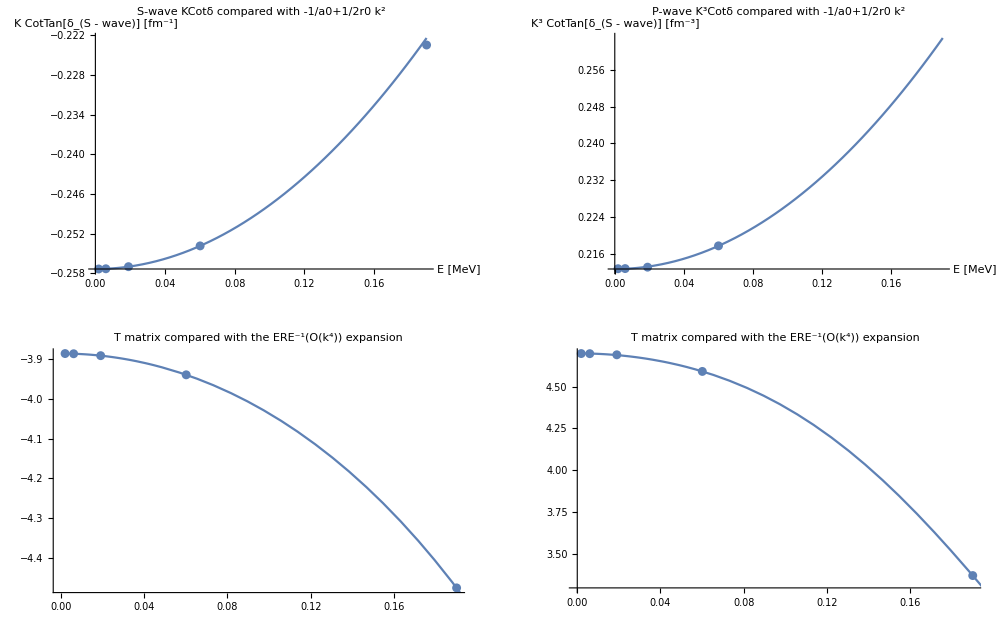

λ = Λ^2/4 = 0.5625 ; R_max = 21.3000:   a0 = 3.88583     r0 = 1.93262     a1 = -4.70072     r1 = 2.77375

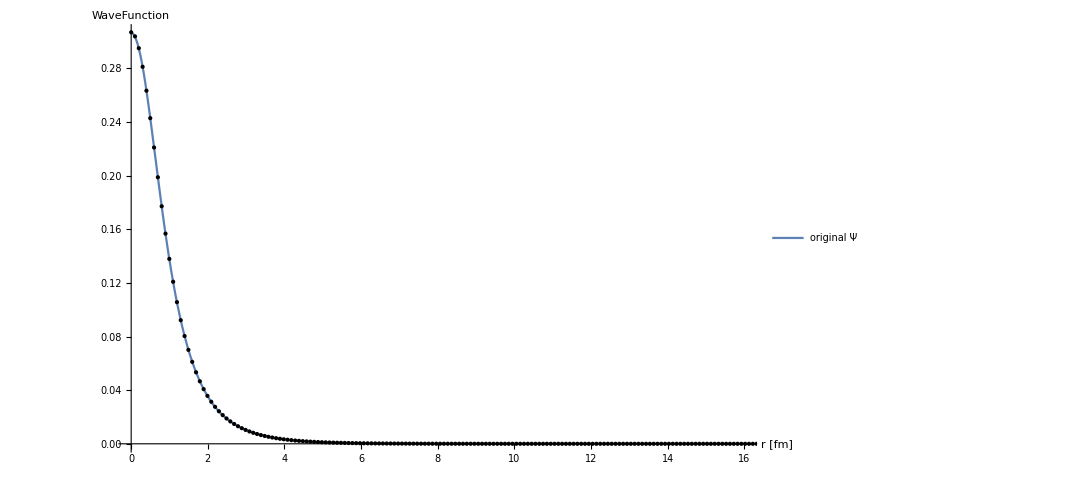

nn=2  nwf=2  λ=1.  C0=-111.302  D0=8.462  core={{0.0454719,0.223235},{0.144003,0.681275},{0.167614,2.09822},{0.00559148,0.0743594}}

General::munfl: Exp[-712.331] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-719.635] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.739] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

S Pole Poitions in momentum: {-1.00201-0.406471 ⅈ,-0.13782+0.406471 ⅈ,0.13782+0.406471 ⅈ,1.00201-0.406471 ⅈ}

S Pole Poitions in energy:   {23.191+22.5209 ⅈ,-4.04271-3.09759 ⅈ,-4.04271+3.09759 ⅈ,23.191-22.5209 ⅈ}

P Pole Poitions in momentum: {-0.176431-0.211928 ⅈ,-0.173813+0.223844 ⅈ,0.173813+0.223844 ⅈ,0.176431-0.211928 ⅈ}

P Pole Poitions in energy:   {-0.381132+2.0675 ⅈ,-0.550053-2.15134 ⅈ,-0.550053+2.15134 ⅈ,-0.381132-2.0675 ⅈ}

-0.268977+0.864896 p^2-1.24879 p^4

0.256264+1.40132 p^2+41.9596 p^4

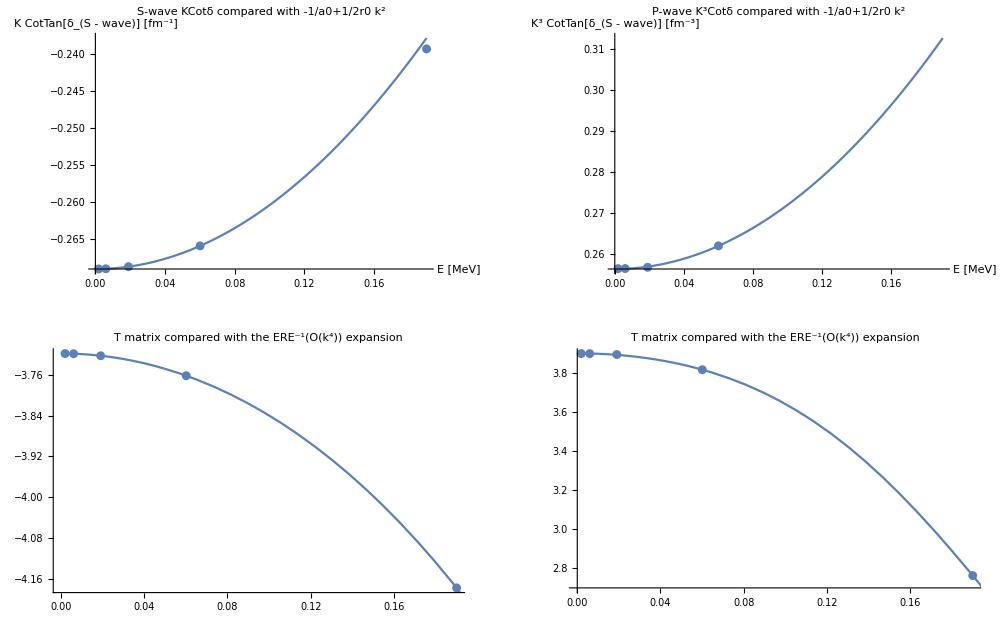

λ = Λ^2/4 = 1.0000 ; R_max = 21.3000:   a0 = 3.7178     r0 = 1.7205     a1 = -3.9025     r1 = 3.11522

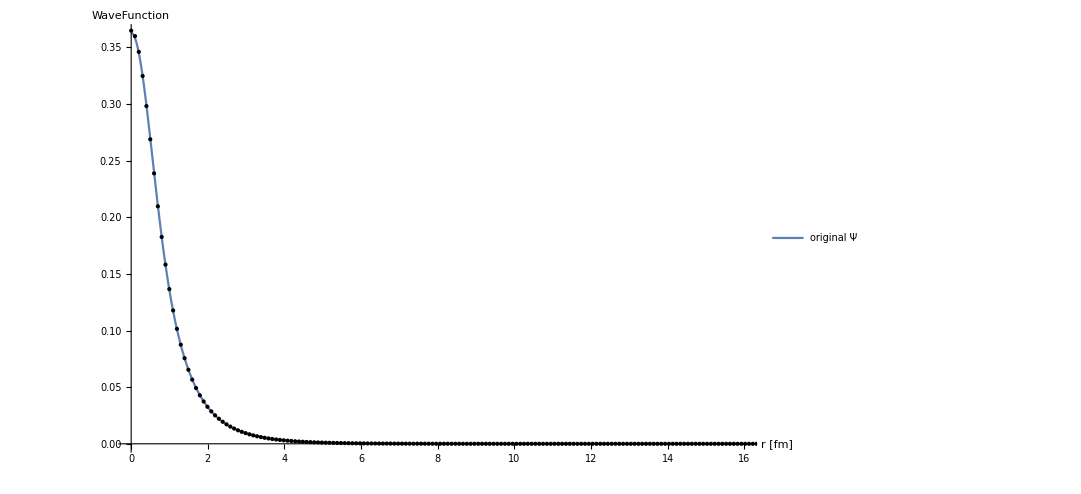

nn=3  nwf=3  λ=2.25  C0=-250.43  D0=123.178  core={{0.296311,2.09955},{0.0174684,0.114449},{0.0621954,0.463435},{0.0601019,0.464489}}

General::munfl: Exp[-716.727] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-755.993] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-714.992] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

S Pole Poitions in momentum: {-1.04035-0.443716 ⅈ,-0.162439+0.443716 ⅈ,0.162439+0.443716 ⅈ,1.04035-0.443716 ⅈ}

S Pole Poitions in energy:   {24.4802+25.5251 ⅈ,-4.7138-3.98545 ⅈ,-4.7138+3.98545 ⅈ,24.4802-25.5251 ⅈ}

P Pole Poitions in momentum: {-0.175099-0.180678 ⅈ,-0.174883+0.185475 ⅈ,0.174883+0.185475 ⅈ,0.175099-0.180678 ⅈ}

P Pole Poitions in energy:   {-0.0548774+1.74934 ⅈ,-0.105534-1.79356 ⅈ,-0.105534+1.79356 ⅈ,-0.0548774-1.74934 ⅈ}

-0.304788+0.762956 p^2-1.06715 p^4

0.428776+0.599935 p^2+104.228 p^4

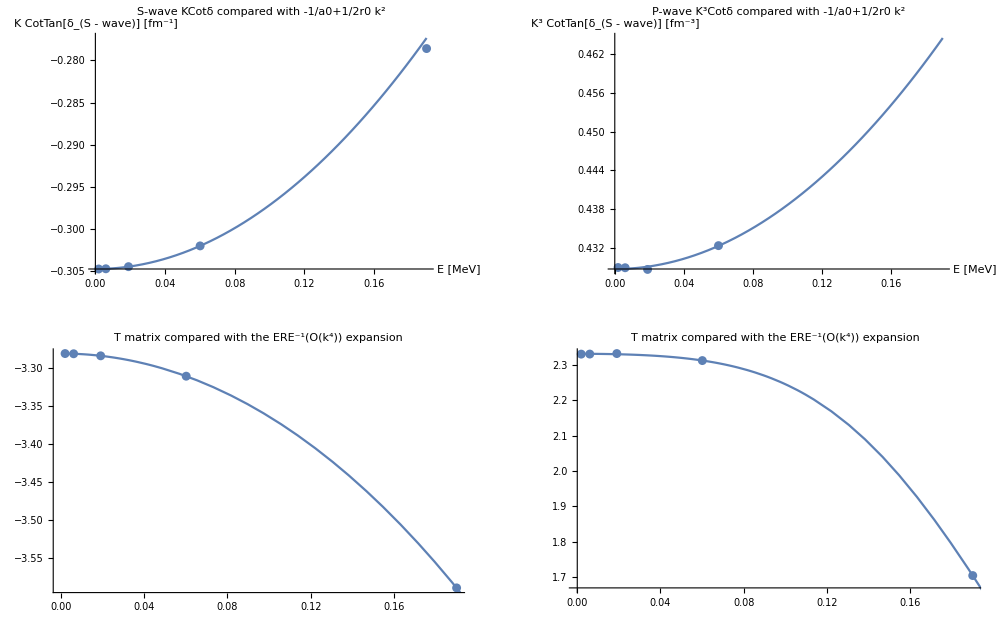

λ = Λ^2/4 = 2.2500 ; R_max = 21.3000:   a0 = 3.28098     r0 = 1.51797     a1 = -2.33247     r1 = 1.9767

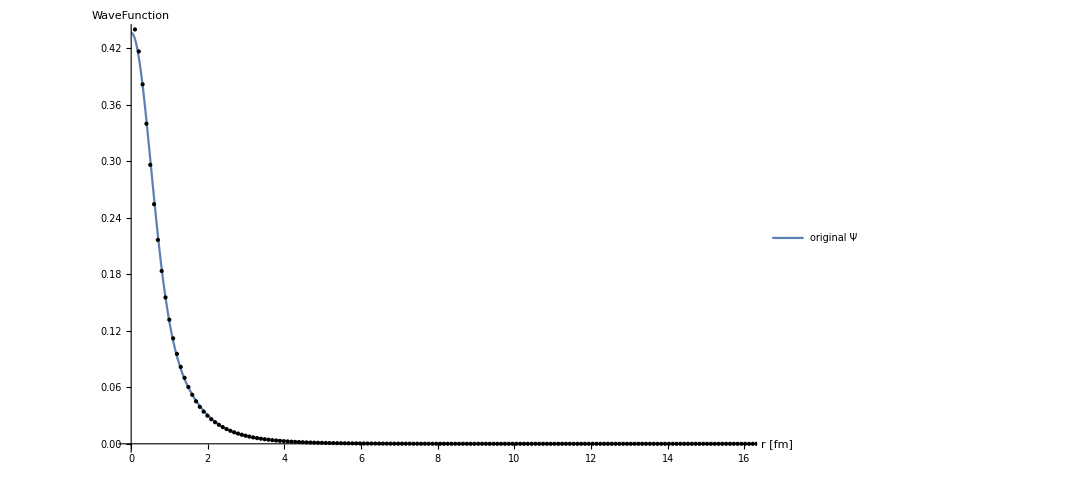

nn=4  nwf=4  λ=4.  C0=-445.21  D0=372.602  core={{0.0931665,0.275992},{0.0345229,1.68181},{0.0252575,1.70581},{0.3285,2.09533}}

General::munfl: Exp[-743.258] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.931] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-724.939] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

S Pole Poitions in momentum: {-1.0441-0.563573 ⅈ,-0.23776+0.563573 ⅈ,0.23776+0.563573 ⅈ,1.0441-0.563573 ⅈ}

S Pole Poitions in energy:   {21.3583+32.5368 ⅈ,-7.21828-7.40922 ⅈ,-7.21828+7.40922 ⅈ,21.3583-32.5368 ⅈ}

P Pole Poitions in momentum: {-0.148519+0.115282 ⅈ,-0.148414-0.114873 ⅈ,0.148414-0.114873 ⅈ,0.148519+0.115282 ⅈ}

P Pole Poitions in energy:   {0.242417-0.946731 ⅈ,0.244151+0.942712 ⅈ,0.244151-0.942712 ⅈ,0.242417+0.946731 ⅈ}

-0.452094+0.438995 p^2-0.858349 p^4

1.52532-21.5612 p^2+1225.11 p^4

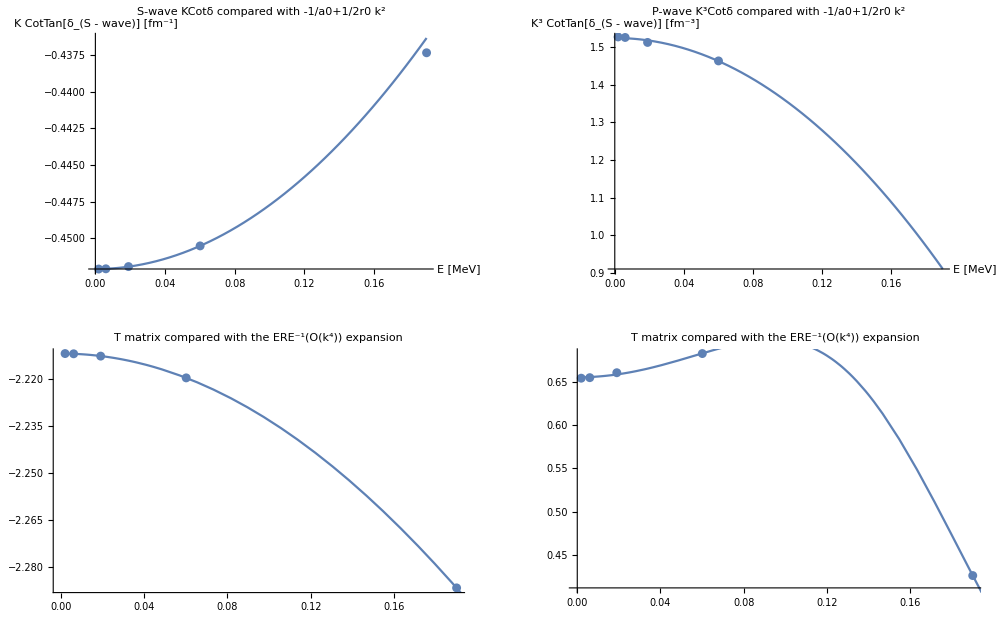

λ = Λ^2/4 = 4.0000 ; R_max = 21.3000:   a0 = 2.21193     r0 = 0.871565     a1 = -0.655832     r1 = -33.9871

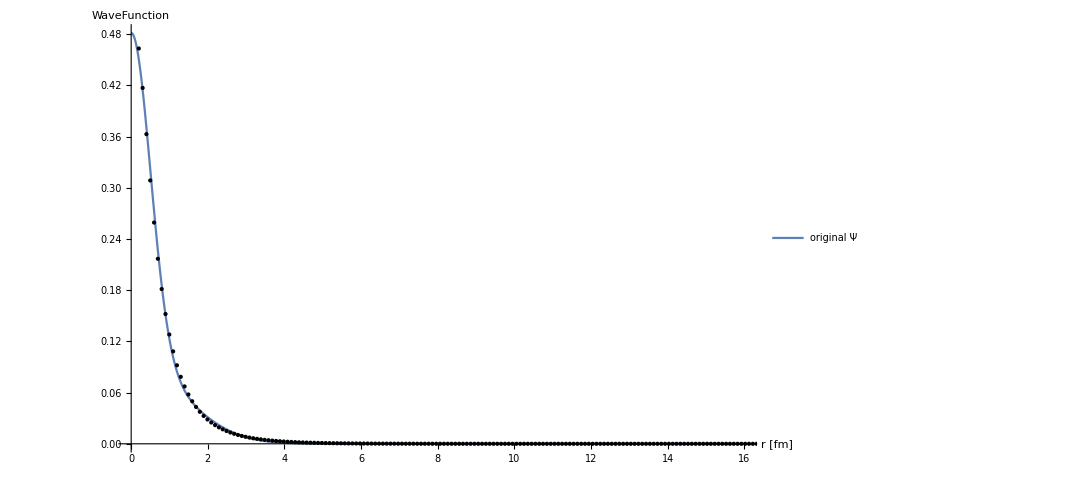

nn=5  nwf=5  λ=9.  C0=-1001.72  D0=1524.25  core={{0.435559,2.1},{0.0424987,0.320602},{0.0424987,0.320602},{0.00605621,0.0769025}}

General::munfl: Exp[-721.504] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-791.854] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-865.477] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-721.504] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-791.854] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-865.477] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

S Pole Poitions in momentum: {-0.804744-0.407972 ⅈ,-0.137585+0.407972 ⅈ,0.137585+0.407972 ⅈ,0.804744-0.407972 ⅈ}

S Pole Poitions in energy:   {13.3031+18.154 ⅈ,-4.0783-3.10373 ⅈ,-4.0783+3.10373 ⅈ,13.3031-18.154 ⅈ}

P Pole Poitions in momentum: {-0.164216-0.182228 ⅈ,-0.163686+0.186714 ⅈ,0.163686+0.186714 ⅈ,0.164216-0.182228 ⅈ}

P Pole Poitions in energy:   {-0.172525+1.65467 ⅈ,-0.223093-1.68994 ⅈ,-0.223093+1.68994 ⅈ,-0.172525-1.65467 ⅈ}

-0.294173+0.650447 p^2-1.94943 p^4

0.413463+1.59023 p^2+111.445 p^4

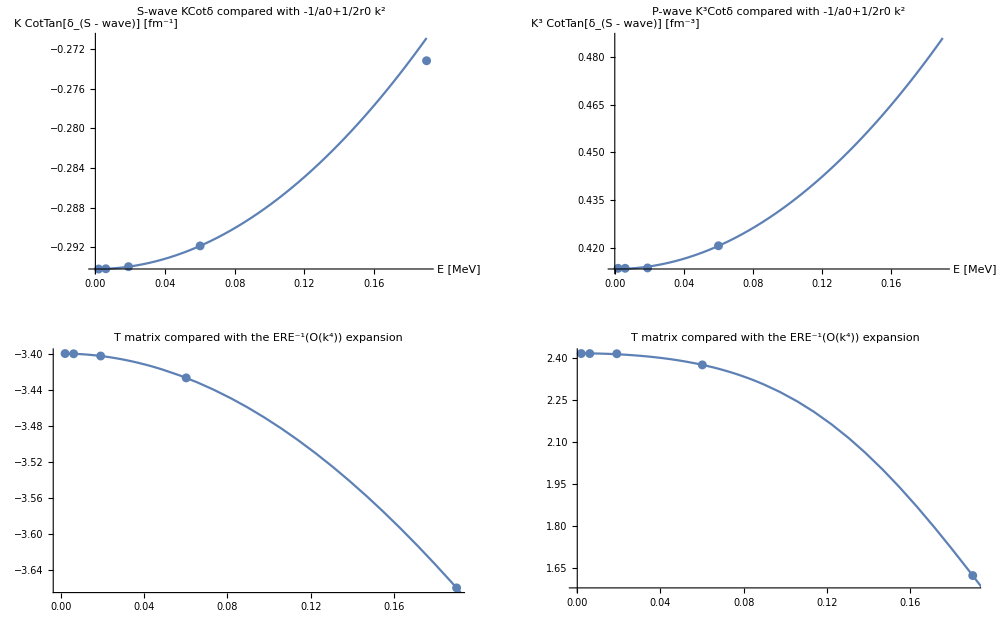

λ = Λ^2/4 = 9.0000 ; R_max = 21.3000:   a0 = 3.39937     r0 = 1.28639     a1 = -2.41888     r1 = 4.01064

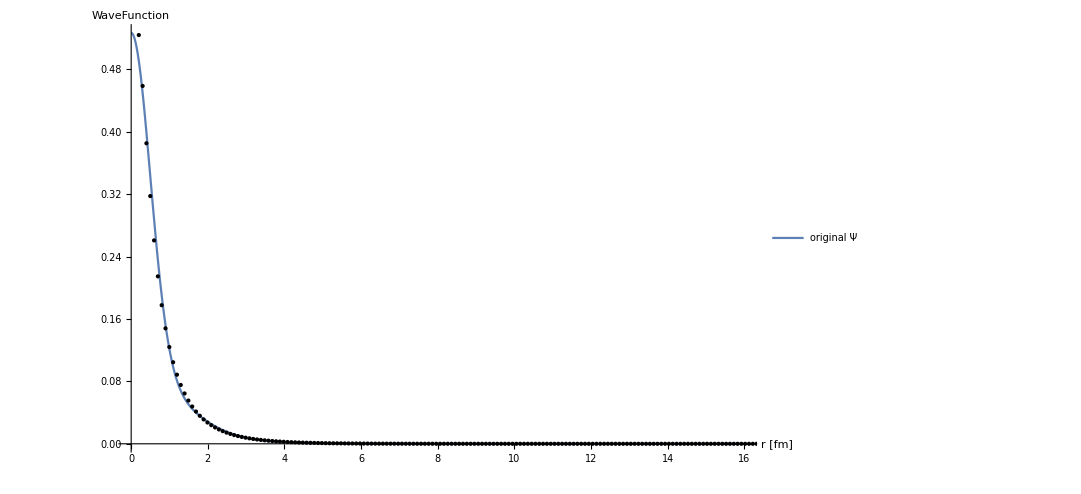

nn=6  nwf=6  λ=16.  C0=-1780.84  D0=4165.55  core={{0.0380442,0.288375},{0.0380442,0.288375},{0.00397222,0.0659831},{0.473733,2.1}}

General::munfl: Exp[-742.857] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-791.557] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-841.802] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

S Pole Poitions in momentum: {-0.733783-0.396921 ⅈ,-0.128055+0.396921 ⅈ,0.128055+0.396921 ⅈ,0.733783-0.396921 ⅈ}

S Pole Poitions in energy:   {10.5306+16.1048 ⅈ,-3.90237-2.8105 ⅈ,-3.90237+2.8105 ⅈ,10.5306-16.1048 ⅈ}

P Pole Poitions in momentum: {-0.159088-0.182322 ⅈ,-0.158437+0.186645 ⅈ,0.158437+0.186645 ⅈ,0.159088-0.182322 ⅈ}

P Pole Poitions in energy:   {-0.219307+1.60384 ⅈ,-0.269125-1.63515 ⅈ,-0.269125+1.63515 ⅈ,-0.219307-1.60384 ⅈ}

-0.292127+0.578507 p^2-2.41303 p^4

0.405879+2.03887 p^2+115.653 p^4

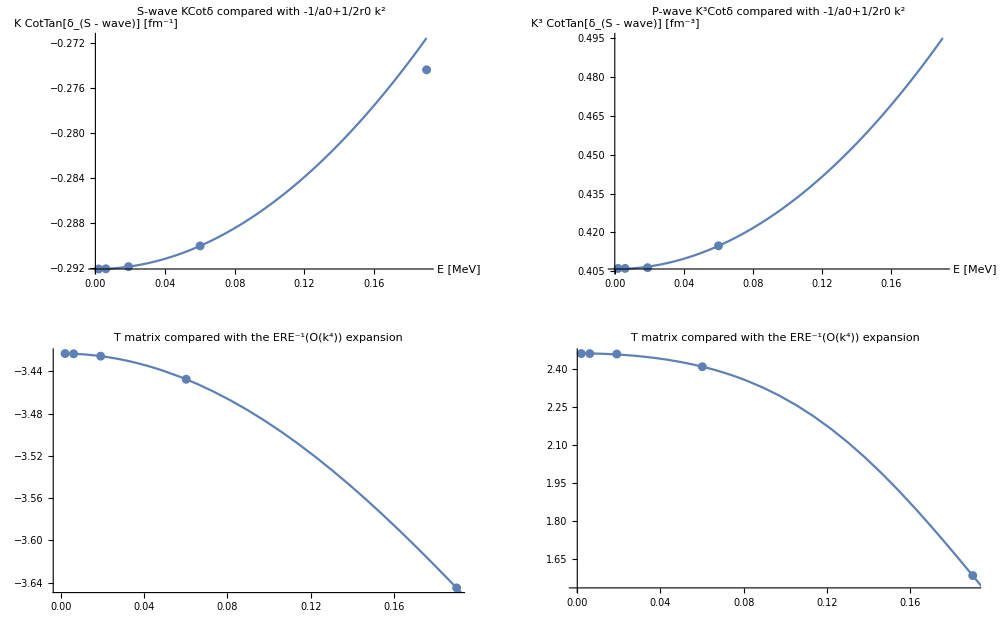

λ = Λ^2/4 = 16.0000 ; R_max = 21.3000:   a0 = 3.42318     r0 = 1.13907     a1 = -2.46409     r1 = 4.93905

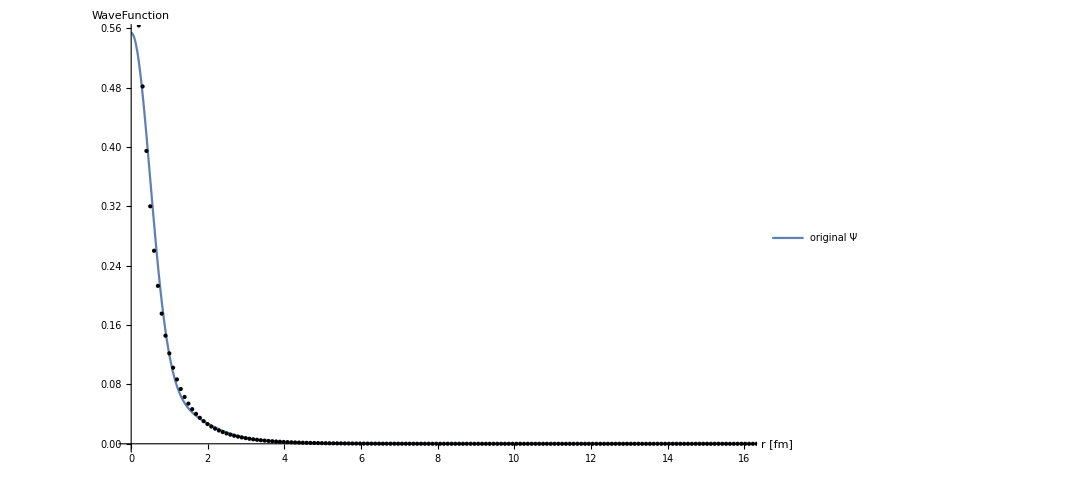

nn=7  nwf=7  λ=25.  C0=-2782.56  D0=9491.9  core={{0.0351526,0.269246},{0.0028255,0.058772},{0.0351526,0.269246},{0.500476,2.1}}

General::munfl: Exp[-710.074] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-758.201] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-807.906] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-710.074] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-758.201] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-807.906] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

S Pole Poitions in momentum: {-0.682251-0.391214 ⅈ,-0.120359+0.391214 ⅈ,0.120359+0.391214 ⅈ,0.682251-0.391214 ⅈ}

S Pole Poitions in energy:   {8.63752+14.7585 ⅈ,-3.83087-2.60362 ⅈ,-3.83087+2.60362 ⅈ,8.63752-14.7585 ⅈ}

P Pole Poitions in momentum: {-0.154766-0.181154 ⅈ,-0.154071+0.185206 ⅈ,0.154071+0.185206 ⅈ,0.154766-0.181154 ⅈ}

P Pole Poitions in energy:   {-0.245073+1.55027 ⅈ,-0.292045-1.57783 ⅈ,-0.292045+1.57783 ⅈ,-0.245073-1.55027 ⅈ}

-0.293666+0.492706 p^2-2.83399 p^4

0.406625+2.39353 p^2+123.412 p^4

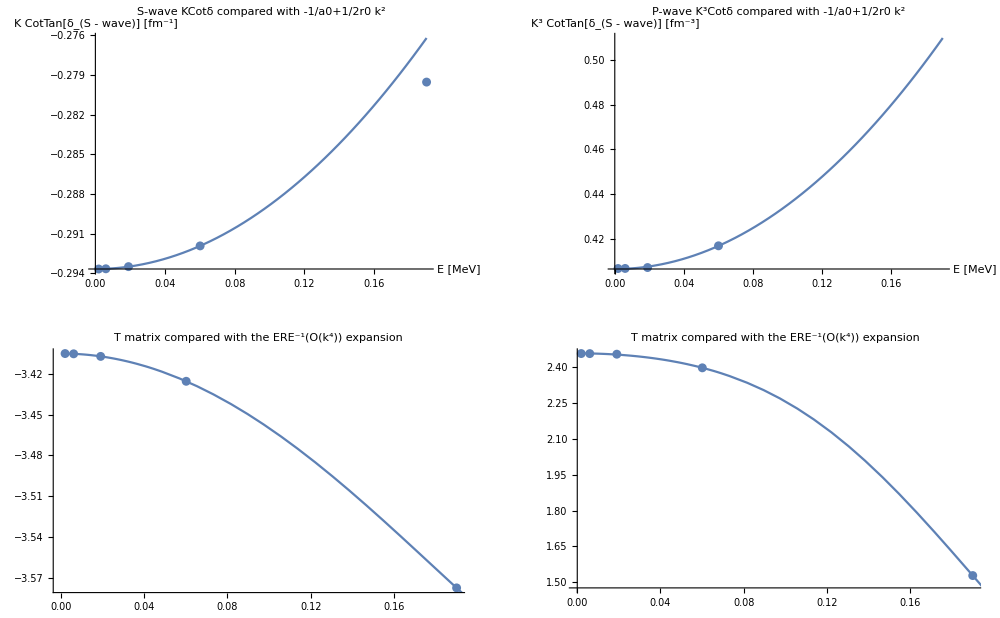

λ = Λ^2/4 = 25.0000 ; R_max = 21.3000:   a0 = 3.40525     r0 = 0.964342     a1 = -2.45959     r1 = 5.70599

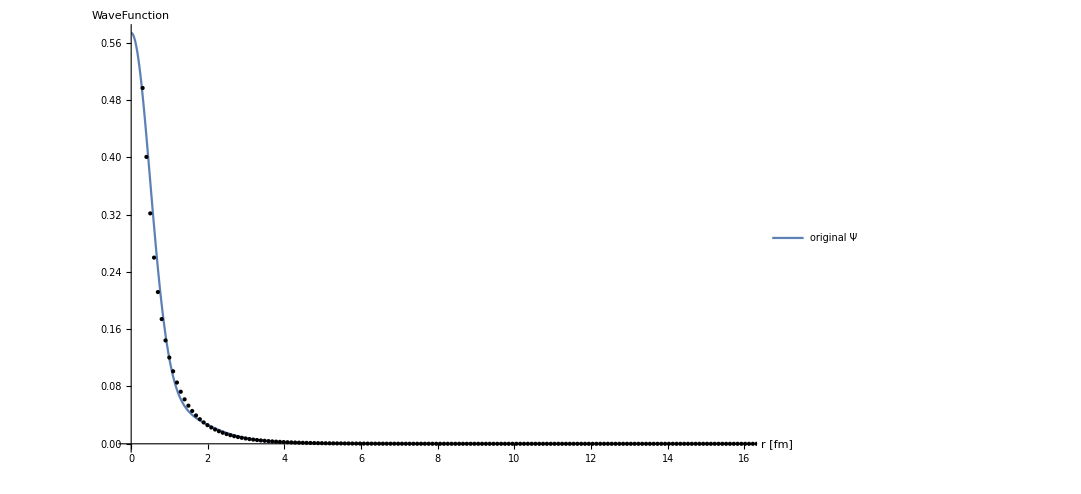

```mathematica
Do[
Do[
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[ll]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
mycore=wfCores[[ll]];
Print["nn=",nn,"  nwf=",ll,"  λ=",λ,"  C0=",C0,"  D0=",D0,"  core=",mycore];
ERE=GetERE[mycore,λ];
PlotERE;
AppendTo[EREs,ERE];
Print["λ = Λ^2/4 = ",NumberForm[λ,nf](*,"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]*)," ; R_max = ",NumberForm[rr,nf],":   a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧];
tmpwfs=Total[#⟦1⟧ⅇ^(-#⟦2⟧ r^2)&/@mycore];
Plot[tmpwfs,{r,rmip,rmap},PlotLegends->{"original Ψ"},PlotRange->Full,Epilog->Map[Point,Mϕ[[ll]]], AxesLabel->{"r [fm]","WaveFunction"},ImageSize->800]//Print;
AppendTo[exportdata,Join[{λ,nGrid,rr},ERE[[;;4]],Polesp,PolesE,Polepp,PolepE,Flatten[mycore]]];
,{ll,lRange}];
,{rr,rGrid}];
Export["/tmp/tmp.dat",exportdata,"Table"];
```

```mathematica
model=a+b/x+c/x^2;
l0=2;
lambdas=exportdata[[All,1]];
a0s=Transpose[{lambdas,exportdata[[All,4]]}];
fita0=model/.FindFit[a0s[[l0;;]],model,{a,b,c},x];
r0s=Transpose[{wflambdas,exportdata[[All,5]]}];
fitr0=model/.FindFit[r0s[[l0;;]],model,{a,b,c},x];
a1s=Transpose[{wflambdas,exportdata[[All,6]]}];
fita1=model/.FindFit[a1s[[l0;;]],model,{a,b,c},x];
r1s=Transpose[{wflambdas,exportdata[[All,7]]}];
fitr1=model/.FindFit[r1s[[l0;;]],model,{a,b,c},x];
legs="R_max="<>ToString[rr];
GraphicsGrid[{{
Show[ListPlot[a0s,PlotLegends->Placed[legs,Above],AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["a_S [\\textrm{fm}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) a_S = "<>ToString[Limit[fita0,x->Infinity]]<>" fm"],Plot[fita0,{x,0,lambdas[[-1]]},ImageSize->Large]],
Show[ListPlot[r0s,AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["r_S [\\textrm{fm}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) r_S = "<>ToString[Limit[fitr0,x->Infinity]]<>" fm"],Plot[fitr0,{x,0,10},ImageSize->Large]]
},{
Show[ListPlot[a1s,PlotLegends->Placed[legs,Above],AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["a_P [\\textrm{fm}^3]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) a_P = "<>ToString[Limit[fita1,x->Infinity]]<>" fm^3"],Plot[fita1,{x,0,lambdas[[-1]]},ImageSize->Large]],
Show[ListPlot[r1s,AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["r_P [\\textrm{fm}^{-1}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) r_P = "<>ToString[Limit[fitr1,x->Infinity]]<>" fm^-1"],Plot[fitr1,{x,0,lambdas[[-1]]},ImageSize->Large]]
}}]
```

-Graphics-

```mathematica
ComplexPlot
```

```mathematica
cplxpoleSp=Transpose[{Re[exportdata[[All,8+#]]],Im[exportdata[[All,8+#]]]}]&/@{0,1,2,3};
cplxpolePp=Transpose[{Re[exportdata[[All,16+#]]],Im[exportdata[[All,16+#]]]}]&/@{0,1,2,3};
GraphicsGrid[{{
Show[ListPlot[#->exportdata[[All,1]],PlotRange->{{-0.5,0.5},{-0.5,0.5}},AxesLabel->{"Re[k_res] [fm^-1]","Im[k_res] [fm^-1]"}]&/@cplxpoleSp]
,
Show[ListPlot[#->exportdata[[All,1]],PlotRange->{{-0.5,0.5},{-0.5,0.5}},AxesLabel->{"Re[k_res] [fm^-1]","Im[k_res] [fm^-1]"}]&/@cplxpolePp]
}}
]
```

-Graphics-

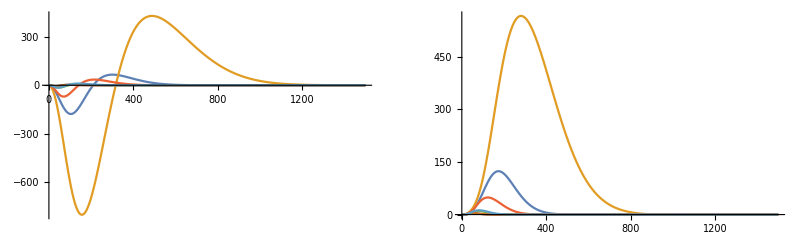

```mathematica
plts={};
pltp={};
Do[
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[nwf]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;
C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
mycore=wfCores[[nwf]];
rMax=15;
eplot=ErangeMeV[[1]];
AppendTo[plts,
Chop[Table[WnolocTF[rr,rr,ErangeMeV[[2]],λ,C0,D0,mycore[[1]][[2]],mycore[[1]][[2]],0,mh2]
,{rr,0.01,rMax,0.01}]]
];
AppendTo[pltp,
Chop[Table[WnolocTF[rr,rr,ErangeMeV[[2]],λ,C0,D0,mycore[[1]][[2]],mycore[[1]][[2]],1,mh2]
,{rr,0.01,rMax,0.01}]]
]
,{nwf,Range[Length[wflambdas]]}]
GraphicsGrid[{{
ListPlot[plts[[1;;7]],Joined->True,PlotRange->Full],
ListPlot[pltp[[1;;7]],Joined->True,PlotRange->Full]
}}]
(*GraphicsGrid[{{
Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[1]][[2]],mycore[[1]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[eplot],"E="<>ToString[eplot]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->Scaled[.8]],Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[2]][[2]],mycore[[2]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[eplot],"E="<>ToString[eplot]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->Scaled[.8]]},{
Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[eplot],"E="<>ToString[eplot]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->Scaled[.8]],Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[2]][[2]],mycore[[1]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[eplot],"E="<>ToString[eplot]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->Scaled[.8]]
}},ImageSize->Full]*)
```

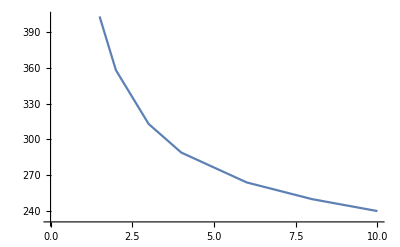

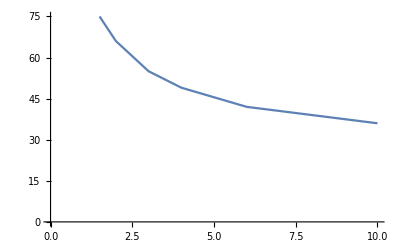

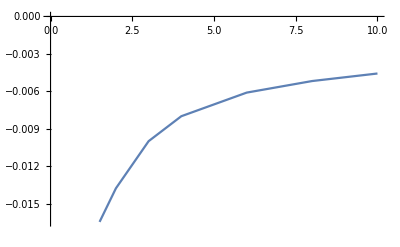

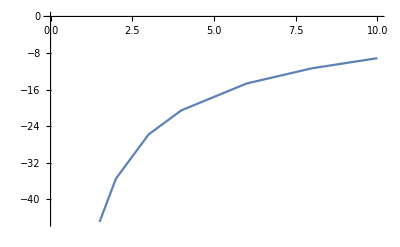

```mathematica
ListPlot[Transpose[{wflambdas,Flatten[Position[#,Min[#]]&/@pltp]}],Joined->True]
ListPlot[Transpose[{wflambdas,Flatten[Position[#,Min[#]]&/@plts]}],Joined->True]
ListPlot[Transpose[{wflambdas,Min[#]&/@pltp}],Joined->True]
ListPlot[Transpose[{wflambdas,Min[#]&/@plts}],Joined->True]
```

```mathematica
vEff[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;

normsqu=NormTF[a00]^2;

Wmat=ConstantArray[0,{Npoints,Npoints}];

Do[
(*If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,*)

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];

wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 
(*Print[(Chop[cij (amat+wmat)])[[1;;4,1;;4]]//MatrixForm];*)
Wmat=Wmat+cij (amat+wmat);

(*]*)
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Dmat=DiagonalMatrix[Table[hDif^2 (-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Dmat+Wmat;
Amat
]
```

```mathematica
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[nwf]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;
C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
mycore=wfCores[[nwf]];
rMax=5;nGrid=80;
pplot=Sqrt[mh2 ErangeMeV[[1]]];
ve=Chop[vEff[rMax,nGrid,pplot,1,λ,C0,D0,mycore,mh2]];
```

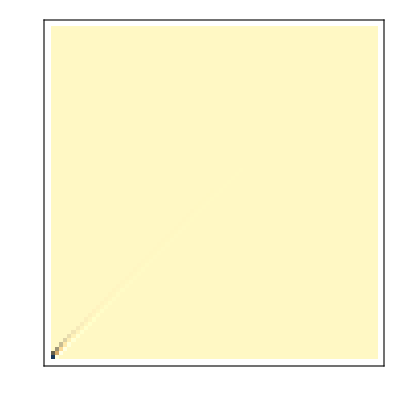

```mathematica
ReliefPlot[ve]
```

```mathematica
ve[[;;5,;;5]]//MatrixForm
```

(-1.9999+3.49497×10^-24 ⅈ | -1.95992×10^-7+5.83338×10^-24 ⅈ | -4.36548×10^-7+3.82753×10^-23 ⅈ | -7.65235×10^-7+8.80287×10^-23 ⅈ | -1.17437×10^-6+5.8628×10^-23 ⅈ
-5.12503×10^-8+1.61049×10^-24 ⅈ | -0.499897+2.30917×10^-23 ⅈ | -4.5379×10^-7+4.94657×10^-23 ⅈ | -7.95376×10^-7+6.03251×10^-23 ⅈ | -1.22046×10^-6+9.2038×10^-23 ⅈ
-5.43967×10^-8+4.6015×10^-24 ⅈ | -2.16243×10^-7+2.33714×10^-23 ⅈ | -0.22212+4.4146×10^-23 ⅈ | -8.4394×10^-7+6.69637×10^-23 ⅈ | -1.29474×10^-6+9.90304×10^-23 ⅈ
-5.85798×10^-8+6.28631×10^-24 ⅈ | -2.32857×10^-7+1.75507×10^-23 ⅈ | -5.18508×10^-7+4.08045×10^-23 ⅈ | -0.124899+7.40627×10^-23 ⅈ | -1.39356×10^-6+1.16391×10^-22 ⅈ
-6.35954×10^-8+3.23485×10^-24 ⅈ | -2.52779×10^-7+1.97249×10^-23 ⅈ | -5.62814×10^-7+4.34204×10^-23 ⅈ | -9.86033×10^-7+8.32233×10^-23 ⅈ | -0.0799002+1.03181×10^-22 ⅈ)